-Graphics-

-Graphics-

-Graphics-

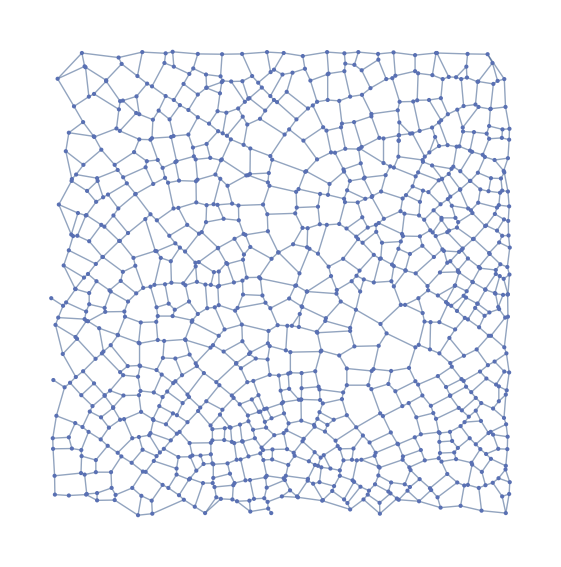

```mathematica
p1=Binarize[-Graphics-];
p2=Thinning[DeleteSmallComponents[ColorNegate[DeleteSmallComponents[p1,300]],300]]
p2=Pruning[p2]
p2=Thinning[p2]
MorphologicalGraph[p2]
(*p2=ColorReplace[p2,White->Transparent];*)
```